# Quantum Mechanics

## Blackbody radiation

### New notations

```mathematica
<<Notation`
```

```mathematica
Symbolize[Subscript[k, B]]
```

```mathematica
Symbolize[Subscript[λ, max]]
```

### Map package symbols

```mathematica
speedOfLight=c;
planckConstant=h;
boltzmannConstant=Subscript[k, B];
u=energyDensity;
```

### Quantities

```mathematica
constantValues={c->Quantity[, "SpeedOfLight"],h->Quantity[, "PlanckConstant"],Subscript[k, B]->Quantity[, "BoltzmannConstant"]}//N
```

{c→1. c,h→1. h,k_B→1. k}

### Energy density

```mathematica
u[λ,𝒯]
```

(8 c h π)/((-1+ⅇ^((c h)/(k_B 𝒯 λ))) λ^5)

```mathematica
Quantity[10.^6,"Pascals"/"Meters"]
```

1.×10^6 Pa/m

1.×10^6 Pa/m

```mathematica
ρ[λ_,𝒯_]=
UnitSimplify[u[λ,𝒯]/Quantity[1.*^6, ("Pascals")/("Meters")]/.constantValues/.{𝒯->Quantity[𝒯,"Kelvins"],λ->Quantity[10^4 λ,"Angstroms"]}]
```

4.99248/((-1+ⅇ^(14387.8/(𝒯 λ))) λ^5)

```mathematica
st[label_]:=Thread[Style[label,"FontFamily"->"Times",FontSize->14]]
```

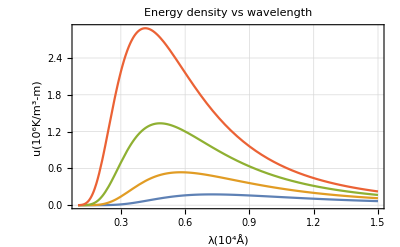

```mathematica
Plot[
Evaluate@
Table[ρ[λ,𝒯],{𝒯,Range[4,7]*1000}],{λ,0.1,1.5},
Frame->True,PlotRange->All,GridLines->Automatic,
PlotLabel->Style["Energy density vs wavelength",16],
FrameLabel->st@{"λ(10^4Å)","u(10^6K/m^3-m)"}
]
```

### Wien' s Displacement Law

```mathematica
dudλ=D[u[λ,𝒯],λ]
```

(8 c^2 ⅇ^((c h)/(k_B 𝒯 λ)) h^2 π)/((-1+ⅇ^((c h)/(k_B 𝒯 λ)))^2 k_B 𝒯 λ^7)-(40 c h π)/((-1+ⅇ^((c h)/(k_B 𝒯 λ))) λ^6)

```mathematica
num=Numerator[dudλ//Together]
```

-8 c h π (-c ⅇ^((c h)/(k_B 𝒯 λ)) h-5 k_B 𝒯 λ+5 ⅇ^((c h)/(k_B 𝒯 λ)) k_B 𝒯 λ)

```mathematica
num/.λ->((c h)/ (Subscript[k, b] x))/𝒯//Simplify
```

(8 c^2 h^2 π (-5 (-1+ⅇ^((x k_b)/k_B)) k_B+ⅇ^((x k_b)/k_B) x k_b))/(x k_b)

```mathematica
eq=5+ⅇ^x(x-5);
```

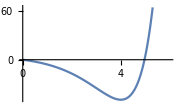

```mathematica
Plot[eq,{x,0,6},ImageSize->Small]
```

```mathematica
sol=FindRoot[eq,{x,5}]
```

{x→4.96511}

```mathematica
Subscript[λ, max]=((c h)/ (Subscript[k, B] x))/𝒯/.sol[[1]]
```

(0.201405 c h)/(k_B 𝒯)

### λ_max for Solar Radiation

```mathematica
Subscript[λ, max]/.constantValues/.𝒯->Quantity[5772., "Kelvins"]
```

0.0000348935 h c/(K k)

```mathematica
UnitConvert[%,"Angstroms"]
```

5020.39 Å